```mathematica
Quit[];
```

# PNW

Alejandro Aviles
avilescervantes@gmail.com

Obtain the non-wiggle linear power spectrum:

call module pknwM[kmin, kmax, Nk, inputPkLinear, hubble] in  file pnw.m 

(Based on the method of  J. Hamann et al, JCAP 07 (2010)022, [arxiv:1003.3999].)

```mathematica
SetDirectory[NotebookDirectory[]];

inputpkfile="pkl_WMAP9.dat";
(*h=0.697;*) 
h=0.6711;(* Hubble *)

outputpknwfile="pkl_nw_WMAP9y.dat";
outputpkfile="pkl_WMAP9y.dat";  (*For Plinear output with the same k's as pNW*)

outkmin=0.00001;  
outkmax=10;
outNk=800;

inputpkT=Import[inputpkfile];  
linesInHeader=1;
inputpkT=Drop[inputpkT,linesInHeader];  (* Delete headers *)


outkmin=inputpkT[[1,1]]  
outkmax=Last[inputpkT[[All,1]]]
outNk=Length@inputpkT;



<<pnw.m  (*In this .m file you can find the module *)


pknwT=pknwM[outkmin,outkmax,outNk,inputpkT,h];
```

0.0000103084

521.888

## Plot

InterpolatingFunction[{{0.0000103084, 521.888}}, <>]

InterpolatingFunction[{{0.0000103084, 521.888}}, <>]

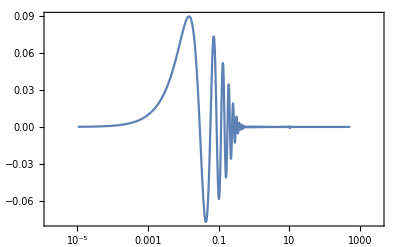

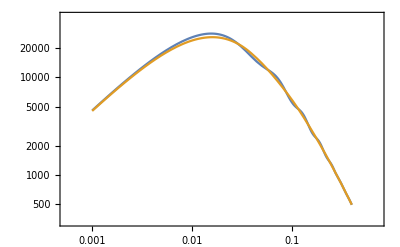

```mathematica
pknw=Interpolation[pknwT]
pk=Interpolation[inputpkT]



prange={outkmin,outkmax};
LogLinearPlot[{(pk[k]-pknw[k])/pknw[k]},{k,prange[[1]],prange[[2]]},Frame->True,PlotRange->All]

LogLogPlot[{pk[k],pknw[k]},{k,0.001,0.4},Frame->True]
```

## Export

```mathematica
outkT=Table[outkmin Exp[(i-1)Log[outkmax/outkmin]/(outNk-1)],{i,1,outNk}];
pkT=Table[{outkT[[i]],pk[outkT[[i]]]},{i,1,outNk}];
Length@pkT
Length@pknwT
Export[outputpknwfile,pknwT]
Export[outputpkfile,pkT]
```

888

888

pkl_nw_WMAP9y.dat

pkl_WMAP9y.dat